# Legendre Polynomials

LegendreP[n,x] gives the Legendre polynomial P_n(x). 
LegendreP[n,m,x] gives the associated Legendre polynomialP_n^m(x).


BesselY[n,z] gives the Bessel function of the second kind Y_n(z) ... The Neumann function

It satisfy the differential equation(1-x^2)(d^2 y/d x^2)-2x(dy/dx)+n(n+1)y=0 that we obtained for example in the solution of the Laplace equation in spherical coordenates.

       Remenber that:

n=l is a number 
       y=y(x)=P(x) where x is the independent variable

#### Traditional form

```mathematica
LegendreP[n,x]//TraditionalForm
LegendreP[n,m,x]//TraditionalForm
```

nx

nmx

#### Solve Equation

Solving the Legendre equation

```mathematica
DSolve[Sin[θ] D[Sin[θ] f'[θ],θ]-m^2 f[θ]==-λ(λ+1)Sin[θ]^2 f[θ],f[θ],θ]
```

{{f[θ]→C[1] LegendreP[λ,m,Cos[θ]]+C[2] LegendreQ[λ,m,Cos[θ]]}}

#### Examples

```mathematica
LegendreP[0,x]
LegendreP[1,x]
LegendreP[2,x]
LegendreP[3,x]
LegendreP[10,x]

LegendreP[3,2,x]
```

1

x

1/2 (-1+3 x^2)

1/2 (-3 x+5 x^3)

1/256 (-63+3465 x^2-30030 x^4+90090 x^6-109395 x^8+46189 x^10)

-15 x (-1+x^2)

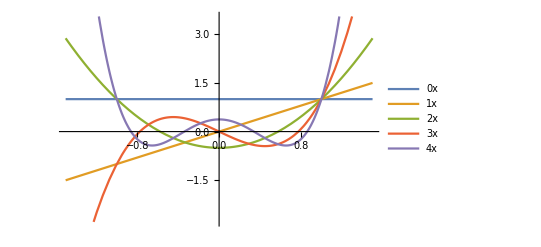

```mathematica
Plot[{LegendreP[0,x],LegendreP[1,x],LegendreP[2,x],LegendreP[3,x],LegendreP[4,x]},{x,-1.5,1.5},PlotLegends->"Expressions"]
```